```mathematica
pts={{0,0}};
```

```mathematica
lreg=1.5;
U=-0.0875/(((-0.5+x)^2+y^2)^(3/2))+0.5/(√((-0.5+x)^2+y^2))+0.5485263464048152 (x^2+y^2)+0.2/(√(0.0001+x^2+y^2))+0.425/(√((0.5+x)^2+y^2))+0.2/(√((-0.5+x)^2+y^2) √((0.5+x)^2+y^2));
```

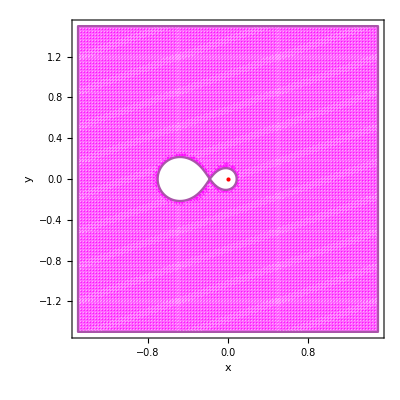

```mathematica
region1=RegionPlot[{2U<=7.662698583004814},{x,-lreg,lreg},{y,-lreg,lreg},BoundaryStyle->Lighter[Purple],PlotPoints->100,Epilog->{Red,PointSize->0.015,Point[pts]},
PlotStyle->Directive[Magenta,Opacity[0.35]],PlotLegends->None,PlotStyle->Directive[Opacity[0.4],Lighter[Black,0.5]],FrameLabel->{Style["x",FontFamily->"Times New Roman",Black,20],Style["y",FontFamily->"Times New Roman",Black,20]},Frame->True,FrameStyle->Directive[Black,15,Thickness[0.004]]]
```